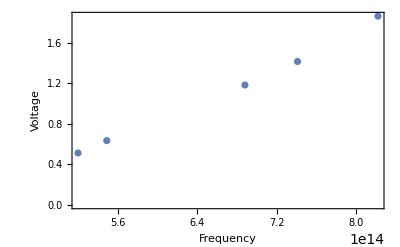

```mathematica
(* this data set is from lab 5 "The photo electric effect" voltage is the "y" value frequency is the  "x" value*)
data1 = {{ 8.22*10^(14),1.864},{7.41*10^(14),1.416},{6.88*10^(14),1.184},{5.49*10^(14),0.635},{5.20*10^(14),0.513}};

ListPlot[data1, PlotRange ->All, Frame -> True, FrameLabel -> {"Frequency", "Voltage"}]
```

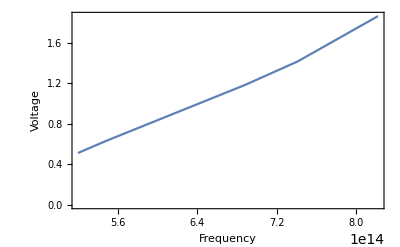

```mathematica
ListPlot[data1, PlotRange ->All, Frame -> True, FrameLabel -> { "Frequency","Voltage"}, Joined -> True]
```

```mathematica
(* This gives the graph equation in the form of y= mx+b; the m= 4.35676*10^-15. This is the planck constant in eV*s*)
```

```mathematica
Fit[data1,{1,x},x]
```

-1.77049+4.35676×10^-15 x

```mathematica
(*This is the planck constant multiplied by "1.602*10^(-19) Joules per eV", this gives the experimentally derived planck constant in Joules* seconds *)
Hcalculate = {4.35676*10^(-15)*1.602*10^(-19)}
```

{6.97953×10^-34}

```mathematica
PercentError = abs[(((6.979*10^(-34))-(6.626*10^(-34)))/(6.626*10^(-34)))*100]
```

```mathematica
abs[5.327497736190749](*5.327%*)
```

ListPlot::prng: Value of option PlotRange -> {{-2.,0},{900000000000000}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.